# Mathématica 1

## Quelques calculs

```mathematica
E^(iPi)
```

ⅇ^iPi

```mathematica
E^(I*Pi)
```

-1

```mathematica
5/2-0.5
```

2.

```mathematica
Pi/2
```

π/2

```mathematica
(I+1)/(I-1)
```

-ⅈ

```mathematica
Sin[Pi/2-1]
```

Cos[1]

```mathematica
Sin'[Pi/2-1]
```

Sin[1]

```mathematica
a+b/c
```

a+b/c

```mathematica
a/b*c
```

(a c)/b

```mathematica
3/2+Pi
```

3/2+π

```mathematica
1.5+Pi
```

4.64159

```mathematica
N[Pi,35]
```

3.1415926535897932384626433832795029

```mathematica
N[Sqrt[1+I]]
```

1.09868+0.45509 ⅈ

```mathematica
N[10^(-20)+1]
```

1.

```mathematica
N[10^(-20)+1.5]
```

1.5

```mathematica
N[E^2,25]
```

7.389056098930650227230427

```mathematica
N[Pi,25]
```

3.141592653589793238462643

```mathematica
N[Log[2],25]
```

0.6931471805599453094172321

```mathematica
N[7/5,10]
```

1.4

```mathematica
N[141/100,10]
```

1.41

```mathematica
N[707/500,10]
```

1.414

```mathematica
N[Sqrt[2],10]
```

1.414213562

## Simplifier

```mathematica
Simplify[(1-x^2)/(1-x)]
```

1+x

```mathematica
Simplify[(x-2)/(Sqrt[x]-Sqrt[2])]
```

(-2+x)/(-√2+√x)

```mathematica
Simplify[(1-Cos[2*t])/(1+Cos[2*t])]
```

Tan[t]^2

```mathematica
Simplify[Cos^(2)[x]-Sin^(2)[x]]
```

Cos^(2[x])-Sin^(2[x])

```mathematica
Simplify[((13+5*Sqrt[17])/2)^(1/3)-((-13+5*Sqrt[17])/2)^(1/3)]
```

(-(-13+5 √17)^(1/3)+(13+5 √17)^(1/3))/2^(1/3)

```mathematica
Simplify[1/(1+1/(1+1/x))]
```

(1+x)/(1+2 x)

## Factoriser, développer

```mathematica
Factor[x^(2)-(a+b)*x+a*b]
```

(a-x) (b-x)

```mathematica
Factor[x^(4)-y^(4)]
```

(x-y) (x+y) (x^2+y^2)

```mathematica
FactorInteger[123456789]
```

{{3,2},{3607,1},{3803,1}}

```mathematica
Expand[(x^(3)*(y-z)^(2)+y^(2)*(-x+z))/(x*(y-z))]
```

-y^2/(y-z)+(x^2 y^2)/(y-z)-(2 x^2 y z)/(y-z)+(y^2 z)/(x (y-z))+(x^2 z^2)/(y-z)

```mathematica
Expand[(x+y)^4]
```

x^4+4 x^3 y+6 x^2 y^2+4 x y^3+y^4

## Complexes

```mathematica
ComplexExpand[E^(I*Pi/4)]
```

(1+ⅈ)/(√2)

```mathematica
ComplexExpand[E^(I*Pi/3)/(2*I)]
```

-ⅈ/4+(√3)/4

```mathematica
Re[x+I*y]
```

-Im[y]+Re[x]

```mathematica
Re[ComplexExpand[x+I*y]]
```

-Im[y]+Re[x]

```mathematica
ComplexExpand[Re[x+i*y]]
```

x+i y

```mathematica
ComplexExpand[Sqrt[E^(-I*Pi/2)]]
```

(1-ⅈ)/(√2)

```mathematica
ComplexExpand[Re[(5+x+I*y)/(-3*I+x+I*y)]]
```

(5 x)/(x^2+(-3+y)^2)+x^2/(x^2+(-3+y)^2)-(3 y)/(x^2+(-3+y)^2)+y^2/(x^2+(-3+y)^2)

```mathematica
ComplexExpand[Im[(5+x+I*y)/(-3*I+x+I*y)]]
```

15/(x^2+(-3+y)^2)+(3 x)/(x^2+(-3+y)^2)-(5 y)/(x^2+(-3+y)^2)

## Résoudre

```mathematica
Solve[8*x+3==0]
```

{{x→-3/8}}

```mathematica
Solve[8*x+3.==0]
```

{{x→-0.375}}

```mathematica
Solve[x^(2)-2*x*Cos[b]+1==0,x]
```

{{x→Cos[b]-ⅈ Sin[b]},{x→Cos[b]+ⅈ Sin[b]}}

```mathematica
Solve[{a*x-y==1&&-x+a*y==0},{x,y}]
```

{{x→a/(-1+a^2),y→1/(-1+a^2)}}

## Graphiques

```mathematica
f[x_]:=x^6-21*x^5+175*x^4-735*x^3+1624*x^2-1764*x+720;
```

f[x_]:=x^6-21 x^5+175 x^4-735 x^3+1624 x^2-1764 x+720

```mathematica
f[0.5]
```

162.422

```mathematica
f[Sqrt[2]]
```

4676-3318 √2

```mathematica
f[z^2]
```

720-1764 z^2+1624 z^4-735 z^6+175 z^8-21 z^10+z^12

```mathematica
Table[f[x],{x,0.1,1.,0.1}]
```

{559.122,426.553,318.482,231.469,162.422,108.574,67.4607,36.9009,14.9737,0.}

```mathematica
Factor[f[x]]
```

(-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x)

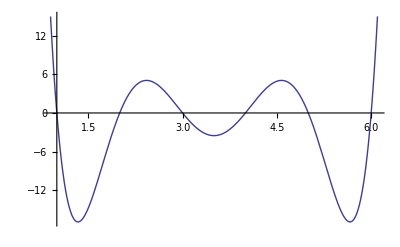

```mathematica
Plot[f[x],{x,0.9,6.1}]
```

```mathematica
Clear[f]
```

```mathematica
f[x_]=x^4
```

x^4

```mathematica
g[x_]=2^x
```

2^x

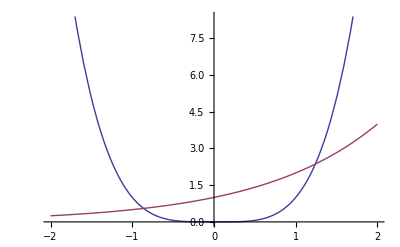

```mathematica
Plot[{f[x],g[x]},{x,-2,2}]
```

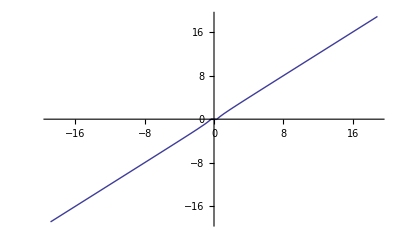

```mathematica
Plot[x^(2)*Sin[1/x],{x,-6*Pi,6*Pi}]
```

```mathematica
Clear[f]
```

```mathematica
Clear[g]
```

```mathematica
p=(2*x^2+x*y-1)^2-(2*x^2-1)^2*(1-x^2)
```

-(1-x^2) (-1+2 x^2)^2+(-1+2 x^2+x y)^2

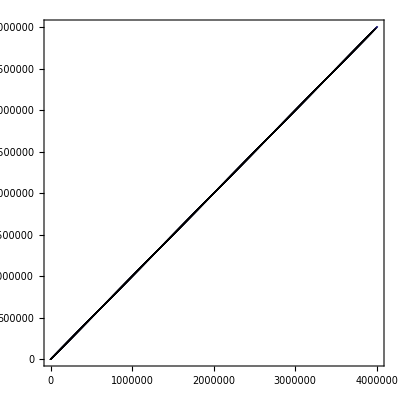

```mathematica
ParametricPlot[{Collect[p,x],Collect[p,y]},{x,-10,10},{y,-10,10}]
```

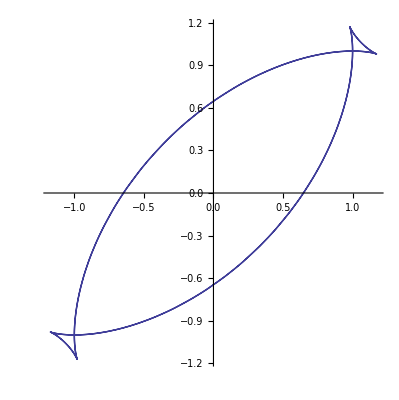

```mathematica
ParametricPlot[{Cos[t]^3+Sin[t],Sin[t]^3+Cos[t]},{t,-2*Pi,2*Pi}]
```

## Calcul de limite. Dériver. Intégrer

```mathematica
Limit[Sin[x]/x, x->0]
```

1

```mathematica
Limit[x^(2)/(x^(2)+3*x),x->Infinity]
```

1

```mathematica
Limit[E^(1/x),x-> 0,Direction->1]
```

0

```mathematica
Limit[Sin[1/x],x-> 0, Direction->-1]
```

Interval[{-1,1}]

```mathematica
D[Tan[x],x]
```

Sec[x]^2

```mathematica
Sin[t]^2
```

Sin[t]^2

```mathematica
Sin^2[t]
```

Sin^(2[t])

```mathematica
D[(x^2+y^2)/(x*y),x]
```

2/y-(x^2+y^2)/(x^2 y)

```mathematica
D[x*Exp[1/x],{x,5}]
```

5 (ⅇ^(1/x)/x^8+(12 ⅇ^(1/x))/x^7+(36 ⅇ^(1/x))/x^6+(24 ⅇ^(1/x))/x^5)+(-ⅇ^(1/x)/x^10-(20 ⅇ^(1/x))/x^9-(120 ⅇ^(1/x))/x^8-(240 ⅇ^(1/x))/x^7-(120 ⅇ^(1/x))/x^6) x

```mathematica
D[x/Exp[y*(a-t)],{t,2}]==x*y^2/.t-> a
```

True

```mathematica
D[x/Exp[y*(a-t)],{t,2}]
```

ⅇ^(-(a-t) y) x y^2

```mathematica
Integer[x^(2)*Sin[x]*Exp[x],{x,-Infinity,Infinity}]
```

Integer[ⅇ^x x^2 Sin[x],{x,-∞,∞}]